## Supercritical Hopf bifurcation

```mathematica
(*Define the vector field in polar coordinates*)
vr[r_,θ_]:=μ r-r^3
vθ[r_,θ_]:=1+ r^2

(*Convert to Cartesian components*)
vx[x_,y_]:=vr[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]-vθ[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]
vy[x_,y_]:=vr[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]+vθ[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]
```

#### Interactive

```mathematica
Manipulate[With[{μval=μμ},
GraphicsRow@{StreamPlot[{vx[x,y],vy[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["Supercritical Hopf  ṙ=μr-r^3, θ̇=1+r^2",FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μμ>0,{Directive[Blue,Thickness[0.01]],Circle[{0,0},Sqrt[μμ]],PointSize[0.03],Red,Point[{0,0}]},{Blue,PointSize[0.03],Point[{0,0}]}]}],Plot[vr[r,0]/.μ->μval,{r,0,3},ImageSize->Small,PlotRange->{All,{-0.2,0.2}},Ticks->None,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})]}],{μμ,-1,1}]
```

#### Interactive Publish

```mathematica
Manipulate[With[{μval=μμ},
GraphicsRow@{StreamPlot[{vx[x,y],vy[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["Supercritical Hopf  ṙ=μr-r^3, θ̇=1+r^2",FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μμ>0,{Directive[Blue,Thickness[0.01]],Circle[{0,0},Sqrt[μμ]],PointSize[0.03],Red,Point[{0,0}]},{Blue,PointSize[0.03],Point[{0,0}]}]}],Plot[vr[r,0]/.μ->μval,{r,0,3},ImageSize->Small,PlotRange->{All,{-0.2,0.2}},Ticks->None,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})]}],{μμ,-1,1}]
CloudDeploy[%,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/3248c921-f5dc-4454-a5c9-0d9f6416595b]

#### Static

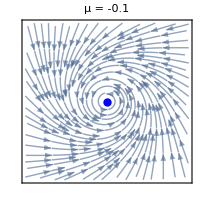
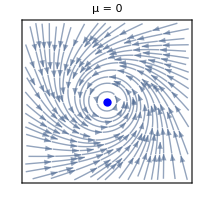
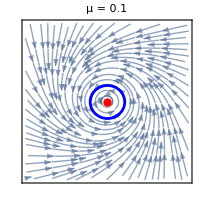
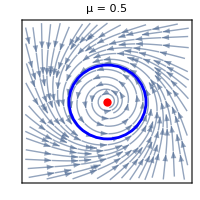

```mathematica
p1a=Row@Table[With[{μval=μμ},
StreamPlot[{vx[x,y],vy[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,ImageMargins->10,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["μ = "<>ToString[μval],FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μval>0,{Directive[Blue,Thickness[0.01]],Circle[{0,0},Sqrt[μval]],PointSize[0.03],Red,Point[{0,0}]},{Blue,PointSize[0.03],Point[{0,0}]}]},ImageSize->200]],{μμ,{-0.1,0,0.1,0.5}}]
```

```mathematica
p1b=Row[Table[With[{μval=μμ},
Plot[vr[r,0]/.μ->μval,{r,0,3},ImageSize->{200,80},AspectRatio->Full,PlotRange->{All,{-0.3,0.3}},ImageMargins->10,Ticks->None(*,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})*)]],{μμ,{-0.1,0,0.1,0.5}}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
p1=Column[{p1a,p1b}]
```

-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"supcrithopf.png",p1]
```

/Users/emad/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Bifurcations/supcrithopf.png

### Eigenvalues

```mathematica
Eigenvalues[{{μ,-ω},{ω,μ}}]
```

{μ-ⅈ ω,μ+ⅈ ω}

## Subcritical Hopf bifurcation without stabilizing term

```mathematica
(*Define the vector field in polar coordinates*)
vra[r_,θ_]:=μ r+r^3
vθa[r_,θ_]:=1+ r^2

(*Convert to Cartesian components*)
vxa[x_,y_]:=vra[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]-vθa[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]
vya[x_,y_]:=vra[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]+vθa[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]
```

#### Interactive

```mathematica
qq=Manipulate[With[{μval=μμ},
GraphicsRow@{StreamPlot[{vxa[x,y],vya[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["Subcritical Hopf  ṙ=μr-r^3, θ̇=1+r^2",FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μμ<0,{Directive[Red,Thickness[0.01]],Circle[{0,0},Sqrt[-μμ]],PointSize[0.03],Blue,Point[{0,0}]},{Red,PointSize[0.03],Point[{0,0}]}]}],Plot[vra[r,0]/.μ->μval,{r,0,3},ImageSize->Small,PlotRange->{All,{-0.4,0.6}},Ticks->None,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})]}],{μμ,-1,1}]
```

```mathematica
CloudDeploy[qq,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/298c4dd2-e741-4ba4-bdb7-c36ae772da1b]

#### Static

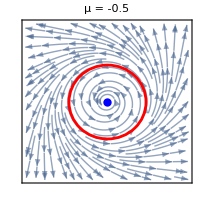
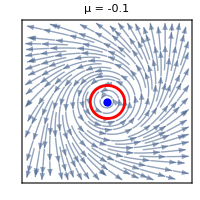
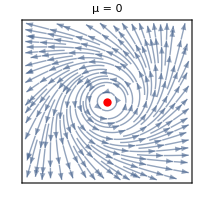
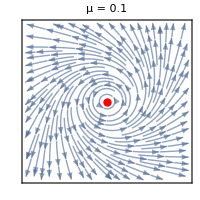

```mathematica
q1a=Row@Table[With[{μval=μμ},
StreamPlot[{vxa[x,y],vya[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,ImageMargins->10,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["μ = "<>ToString[μval],FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μμ<0,{Directive[Red,Thickness[0.01]],Circle[{0,0},Sqrt[-μμ]],PointSize[0.03],Blue,Point[{0,0}]},{Red,PointSize[0.03],Point[{0,0}]}]},ImageSize->200]],{μμ,{-0.5,-0.1,0,0.1}}]
```

```mathematica
q1b=Row[Table[With[{μval=μμ},
Plot[vra[r,0]/.μ->μval,{r,0,3},ImageSize->{200,80},AspectRatio->Full,PlotRange->{All,{-0.3,0.3}},ImageMargins->10,Ticks->None(*,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})*)]],{μμ,{-0.5,-0.1,0,0.1}}]]
```

-Graphics--Graphics--Graphics--Graphics-

```mathematica
q1=Column[{q1a,q1b}]
```

-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"subcrithopf.png",q1]
```

/Users/emad/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Bifurcations/subcrithopf.png

## Higher-order subcritical Hopf bifurcation

At μ = 0, a subcritical Hopf bifurcation occurs. But at a negative value of μ, a saddle-node bifurcation occurs.

```mathematica
(*Define the vector field in polar coordinates*)
vr2[r_,θ_]:=μ r+r^3-r^5
vθ2[r_,θ_]:=1+ r^2

(*Convert to Cartesian components*)
vx2[x_,y_]:=vr2[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]-vθ2[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]
vy2[x_,y_]:=vr2[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]+vθ2[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]
```

#### Manipulate

```mathematica
p11=Manipulate[With[{μval=μμ},Module[{sol},
sol=Solve[(vr2[r,θ]/.μ->μval)==0,r,PositiveReals];
GraphicsRow@{StreamPlot[{vx2[x,y],vy2[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["Subcritical Hopf  ṙ=μr+r^3-r^5, θ̇=1+r^2",FontFamily->"EB Garamond",FontSize->20],Epilog->{PointSize[0.03],Red,Point[{0,0}],Orange,PointSize[0.03],Point[{0,0}],If[Length[sol]≠0,{Directive[Orange,Thickness[0.01]],Circle[{0,0},r]/.sol}]}],Plot[vr2[r,0]/.μ->μval,{r,0,3},ImageSize->{200,120},AspectRatio->6/8,PlotRange->{{0,1.5},{-0.6,0.6}},Ticks->None,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})]}]],{μμ,-1,1}]
```

```mathematica
CloudDeploy[p11,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/a9538aa1-13a0-404a-9057-a446efad6505]

#### Static

```mathematica
μvals2={-0.5,-0.25,-0.23,-0.19,-0.1,0,0.5};
```

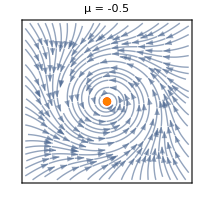
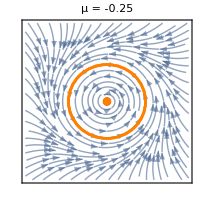
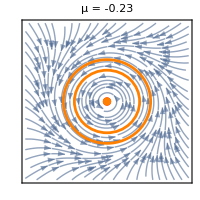
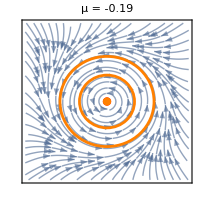
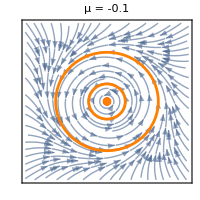
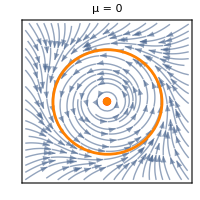
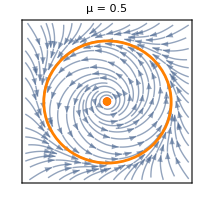

```mathematica
p2a=Row@Table[With[{μval=μμ},Module[{sol},
sol=Solve[(vr2[r,θ]/.μ->μval)==0,r,PositiveReals];
StreamPlot[{vx2[x,y],vy2[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,PlotRangePadding->None,ImageMargins->10,StreamStyle->Opacity[0.6],FrameTicks->None,StreamScale->Medium,PlotLabel->Style["μ = "<>ToString[μval],FontFamily->"EB Garamond",FontSize->20],Epilog->{PointSize[0.03],Red,Point[{0,0}],Orange,PointSize[0.03],Point[{0,0}],If[Length[sol]≠0,{Directive[Orange,Thickness[0.01]],Circle[{0,0},r]/.sol}]},ImageSize->200]]],{μμ,μvals2}]
```

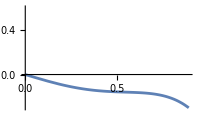
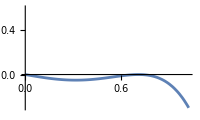
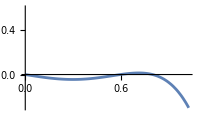
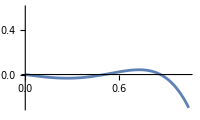
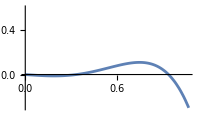
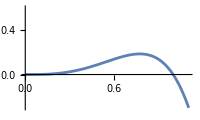
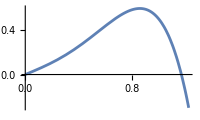

```mathematica
p2b=Row[Table[With[{μval=μμ},
Plot[vr2[r,0]/.μ->μval,{r,0,3},ImageSize->{200,120},AspectRatio->Full,ImageMargins->10,PlotRange->{All,{-0.3,0.6}},Ticks->None(*,AxesLabel->(Style[#,FontFamily->"EB Garamond",FontSize->20]&/@{"r","ṙ"})*)]],{μμ,μvals2}]]
```

```mathematica
p2=Column[{p2a,p2b}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Export[NotebookDirectory[]<>"higherordersubcrithopf.png",p2]
```

/Users/emad/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Bifurcations/higherordersubcrithopf.png

## Infinite-period bifurcation

```mathematica
(*Define the vector field in polar coordinates*)
vr3[r_,θ_]:=r(1-r^2)
vθ3[r_,θ_]:=μ-Sin[θ]

(*Convert to Cartesian components*)
vx3[x_,y_]:=vr3[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]-vθ3[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]
vy3[x_,y_]:=vr3[Sqrt[x^2+y^2],ArcTan[x,y]] Sin[ArcTan[x,y]]+vθ3[Sqrt[x^2+y^2],ArcTan[x,y]] Cos[ArcTan[x,y]]
```

#### Manipulate

```mathematica
ppp=Manipulate[With[{μval=μμ},Module[{sol},
If[μval<1,sol=FindRoot[(vθ3[r,θ]/.μ->μval),{θ,0}]];
StreamPlot[{vx3[x,y],vy3[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,PlotLabel->Style["∞-period Bifurc.  ṙ = r (1-r^2) ,  θ̇ = μ - Sin θ",FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μval<1,{PointSize[0.03],Point[FromPolarCoordinates[{1,(π-θ)/.sol}]],Directive[Blue],Point[FromPolarCoordinates[{1,θ/.sol}]]}],Directive[Blue],Circle[{0,0},1]}]]],{μμ,0,2}]
```

```mathematica
CloudDeploy[ppp,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/bdfe30c4-6e83-4a9e-b86a-56f4e2e57bc9]

#### Static images

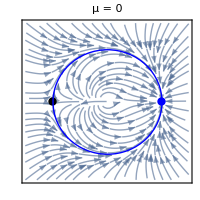
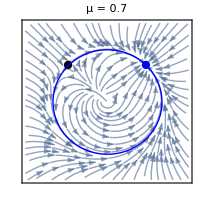
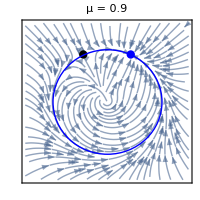
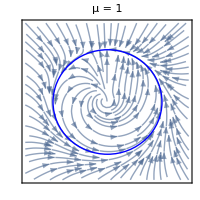
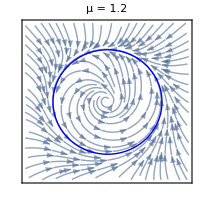

```mathematica
qqqq=Row[Table[With[{μval=μμ},Module[{sol},
If[μval<1,sol=FindRoot[(vθ3[r,θ]/.μ->μval),{θ,0}]];
StreamPlot[{vx3[x,y],vy3[x,y]}/.μ->μval,{x,-1.5,1.5},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,ImageSize->{200,200},PlotLabel->Style["μ = "<>ToString[μval],FontFamily->"EB Garamond",FontSize->20],Epilog->{If[μval<1,{PointSize[0.03],Point[FromPolarCoordinates[{1,(π-θ)/.sol}]],Directive[Blue],Point[FromPolarCoordinates[{1,θ/.sol}]]}],Directive[Blue],Circle[{0,0},1]}]]],{μμ,{0,0.7,0.9,1,1.2}}]]
```

```mathematica
Export[NotebookDirectory[]<>"infperiod.png",qqqq]
```

/Users/emad/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Bifurcations/infperiod.png

## Homoclinic Bifurcation

```mathematica
(*Define the vector field in Cartesian coordinates*)
vx4[x_,y_]:=y
vy4[x_,y_]:=μ y + x - x^2+x y
```

#### Manipulate

```mathematica
qqqqq=Manipulate[With[{μval=μμ},Module[{sol},
StreamPlot[{vx4[x,y],vy4[x,y]}/.μ->μval,{x,-0.5,2.5},{y,-1,1},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Small,AspectRatio->Automatic,StreamScale->Medium,PlotLabel->Style["Homoclinic Bifurc.  ẋ = y, ẏ = μy + x - x^2+xy",FontFamily->"EB Garamond",FontSize->20],Epilog->{PointSize[0.02],Point[{0,0}],Point[{1,0}]}]]],{μμ,-1,1}]
```

```mathematica
CloudDeploy[qqqqq,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/8d0032f3-f406-4d65-bccd-a24daa87b9e9]

```mathematica
{x[#][t],y[#][t]}&/@{1,2,3}
```

{{x[1][t],y[1][t]},{x[2][t],y[2][t]},{x[3][t],y[3][t]}}

#### Static

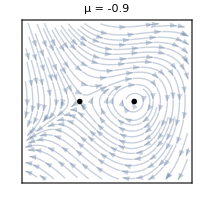
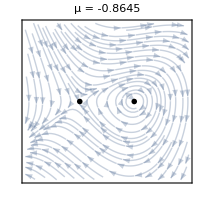
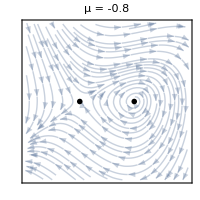

```mathematica
new=Row[Table[With[{μval=μμ},Module[{sol},
StreamPlot[{vx4[x,y],vy4[x,y]}/.μ->μval,{x,-1,2},{y,-1.5,1.5},StreamColorFunction->None,StreamStyle->Opacity[0.3],PlotRangePadding->None,FrameTicks->None,StreamScale->Medium,ImageSize->{200,200},PlotLabel->Style["μ = "<>ToString[μval],FontFamily->"EB Garamond",FontSize->20],Epilog->{PointSize[0.02],Point[{0,0}],Point[{1,0}]}]]],{μμ,{-0.9,-0.8645,-0.8}}]]
```

```mathematica
Export[NotebookDirectory[]<>"homoclinic.png",new]
```

/Users/emad/Library/CloudStorage/GoogleDrive-emasroo1@swarthmore.edu/My Drive/Teaching/Spring 2025/E91/Demonstrations/Bifurcations/homoclinic.png

#### Dynamics

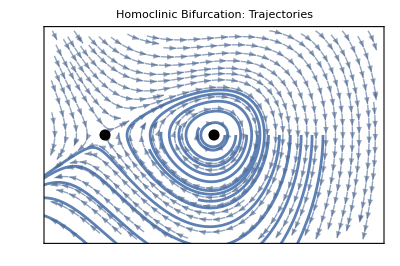

```mathematica
With[{μval=-0.92},Module[{sys,sol,phaseportrait,trajs},
sys={x'[t]==vx4[x[t],y[t]],y'[t]==vy4[x[t],y[t]]}/.μ->μval;
sol=ParametricNDSolve[{sys,x[0]==x0,y[0]==0},{x,y},{t,0,100},x0];
phaseportrait=StreamPlot[{vx4[x,y],vy4[x,y]}/.μ->μval,{x,-0.5,2.5},{y,-1,1},StreamColorFunction->None,StreamStyle->Opacity[0.6],PlotRangePadding->None,FrameTicks->None,StreamScale->Small,AspectRatio->Automatic,StreamScale->Medium,PlotLabel->Style["Homoclinic Bifurcation: Trajectories",FontFamily->"EB Garamond",FontSize->20],Epilog->{PointSize[0.02],Point[{0,0}],Point[{1,0}]}];
trajs=ParametricPlot[{x[#][t],y[#][t]}&/@Table[i,{i,1.1,2,0.1}]/.sol,{t,0,10},PlotRange->{{-0.5,2.5},{-1,1}},AspectRatio->Automatic,Frame->True];
Show[phaseportrait,trajs]
]
]
```